```mathematica
gT samp=10^(-2);(*sampling period*)
```

```mathematica
g f0=10;(*frequency*)
```

```mathematica
u[t_]=Exp[I*2Pi*g f0*t];(*continuous time input wave*)
```

```mathematica
v[t_]=Integrate[u[τ],{τ,0,t}](*ideal integral wave*)
```

-(ⅈ (-1+ⅇ^(20 ⅈ π t)))/(20 π)

```mathematica
x dd[n_]=gT samp*(1-Exp[I*2Pi*g f0*gT samp*n])/(1-Exp[I*2Pi*g f0*gT samp])(*integrated discrete signal by Euler method*)
```

(1-ⅇ^((ⅈ n π)/5))/(100 (1-ⅇ^((ⅈ π)/5)))

```mathematica
x d[t_]:=x dd[Floor[t/gT samp]](*continuous-time extension of x d*)
```

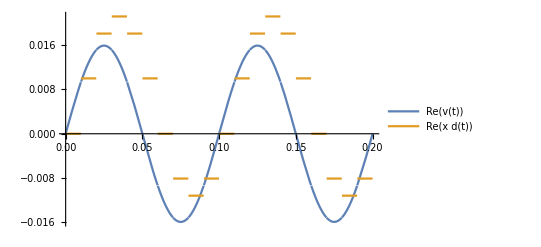

```mathematica
Plot[{Re[v[t]],Re[x d[t]]},{t,0,2/g f0},PlotLegends->"Expressions"]
```

```mathematica
gN=200;gT int=gN*gT samp;(*integration time*)
```

```mathematica
V[f_]=Integrate[v[t]*Exp[-I*2Pi*f*t],{t,0,gT int}]/gT int
```

(1-ⅇ^(-4 ⅈ f π))/(2 (40 f π^2-4 f^2 π^2))

```mathematica
AbsArg[Limit[V[f],f->g f0]]
```

{1/(20 π),-π/2}

```mathematica
N[%]
```

{0.0159155,-1.5708}

```mathematica
X d[f_]=(1-Exp[-I*2Pi*f*gT samp])/(1-Exp[I*2Pi*g f0*gT samp])/(I*2Pi*f)/gN*((1-Exp[-I*2Pi*f*gT samp*gN])/(1-Exp[-I*2Pi*f*gT samp])-(1-Exp[-I*2Pi*(f-g f0)*gT samp*gN])/(1-Exp[-I*2Pi*(f-g f0)*gT samp]))(*equals to Integrate[y[t]*Exp[-I*2Pi*f*t],{t,0,gT int}]/gT int*)
```

-(ⅈ (1-ⅇ^(-1/50 ⅈ f π)) (-(1-ⅇ^(-4 ⅈ (-10+f) π))/(1-ⅇ^(-1/50 ⅈ (-10+f) π))+(1-ⅇ^(-4 ⅈ f π))/(1-ⅇ^(-1/50 ⅈ f π))))/(400 (1-ⅇ^((ⅈ π)/5)) f π)

```mathematica
N[AbsArg[Limit[X d[f],f->g f0]]]
```

{0.0159155,-2.19911}

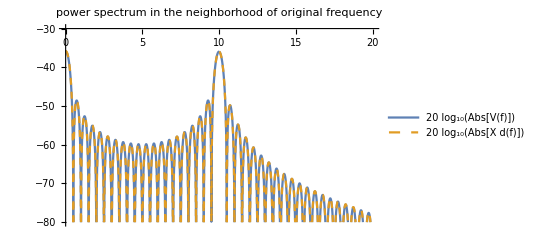

```mathematica
Plot[{20Log10[Abs[V[f]]],20Log10[Abs[X d[f]]]},{f,0,2g f0},PlotRange->{-80,-30},PlotStyle->{Normal,Dashed},PlotLegends->"Expressions",PlotLabel->"power spectrum in the neighborhood of original frequency"]
```

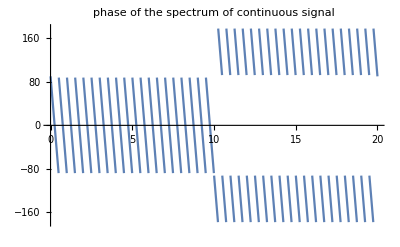

```mathematica
Plot[Arg[V[f]]*180/Pi,{f,0,2g f0},PlotRange->Full,PlotLabel->"phase of the spectrum of continuous signal"]
```

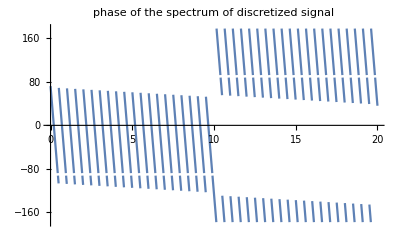

```mathematica
Plot[Arg[X d[f]]*180/Pi,{f,0,2g f0},PlotRange->Full,PlotLabel->"phase of the spectrum of discretized signal"]
```

```mathematica
Arg[X d[10.001]]*180/Pi(*phase difference near g f*)
```

-126.362

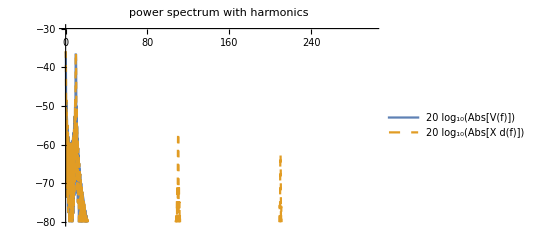

```mathematica
Plot[{20Log10[Abs[V[f]]],20Log10[Abs[X d[f]]]},{f,0,3/gT samp},PlotRange->{-80,-30},PlotStyle->{Normal,Dashed},PlotLegends->"Expressions",PlotLabel->"power spectrum with harmonics"]
```